```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/thermodynamic_integration_analysis/GibbsBog/nov16_x_free_4_longRun_4.8_4_3_v1v2_noholdcutoffs/2MEAM_Hessian_run"];
dudlFiles={"T_all_vol_dUdL"};
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number}],{i,1,1}];
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11];
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,2}];
```

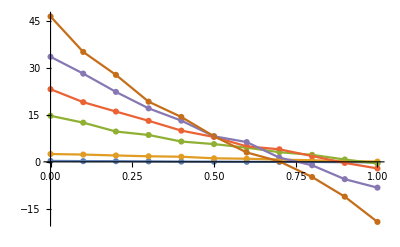

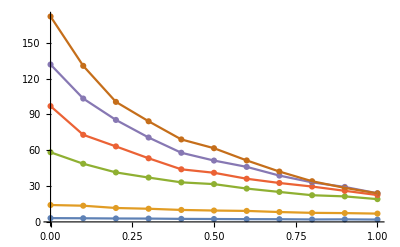

```mathematica
Show[{ListPlot@dudlAll[[1]],ListLinePlot@dudlAll[[1]]}]
Show[{ListPlot@dudlAll[[2]],ListLinePlot@dudlAll[[2]]}]
```

```mathematica
dudlAllFit1=Table[Table[Fit[dudlAll[[vol]][[temp]],{1L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit3=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit4=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^4,L^2,L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
```

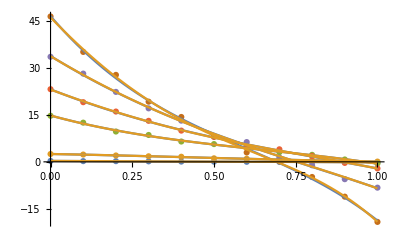

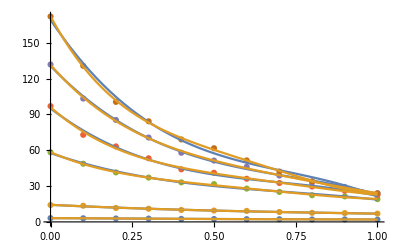

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[{dudlAllFit3[[1]],dudlAllFit4[[1]]},{L,0,1}]]
Show[ListPlot[dudlAll[[2]]],Plot[{dudlAllFit3[[2]],dudlAllFit4[[2]]},{L,0,1}]]
```

```mathematica
bound1=0;bound2=1; 

(*Solver 1 - standard *)
mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
mvtSolverNum[arg_]:=mvtSolver[arg][[1]][[1]][[2]][[1]]
(*Integrator*)
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
(*Solver 2 - midpoint*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
(*Solver 3 - l1 l2 norm CS inpsired solver *)
weightedMVT[fun_,mu_,nu_,midpoint_]:=nu*NMinimize[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,x]
mvtNumWeight[arg_,mu_,nu_,midpoint_]:={mvtSolver[arg][[1]][[1]][[2]][[1]],weightedMVT[arg,mu,nu,midpoint]}
```

```mathematica
weightedMVT[dudlAllFit4[[1]][[1]],0.01,0.5]
weightedMVT[dudlAllFit4[[1]][[2]],0.01,0.5]
mvtNumWeight[dudlAllFit4[[1]][[2]],0.01,0.5]
```

weightedMVT[-0.72811-0.253383 L-1.68118 L^2+3.41733 L^3-1.98642 L^4,0.01,0.5]

weightedMVT[-0.169547-2.11935 L-0.492537 L^2-0.498969 L^3+0.762048 L^4,0.01,0.5]

mvtNumWeight[-0.169547-2.11935 L-0.492537 L^2-0.498969 L^3+0.762048 L^4,0.01,0.5]

```mathematica
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],0.01,1,0.5],{i,1,6}]//TableForm
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],200,1,0.5],{i,1,6}]//TableForm
```

0.464851 | 0.0000116122
x→0.466968
0.489813 | 1.03647×10^-6
x→0.489826
0.457792 | 0.0000178138
x→0.457795
0.457672 | 0.0000179162
x→0.457673
0.466496 | 0.0000112251
x→0.466496
0.455367 | 0.0000199208
x→0.455367

0.464851 | 0.000179859
x→0.499975
0.489813 | 0.000761515
x→0.499627
0.457792 | 0.155591
x→0.481712
0.457672 | 0.264912
x→0.468761
0.466496 | 0.199072
x→0.470297
0.455367 | 0.369329
x→0.458634

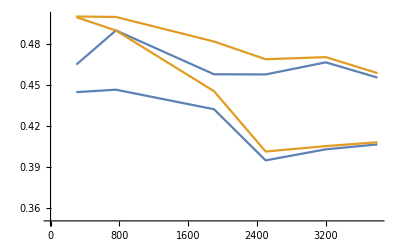

```mathematica
dataMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
dataWMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
Show[Table[ListLinePlot[{dataMVT4[[i]],dataWMVT4[[i]]},PlotRange->{{0,3800},{0.35,0.5}}],{i,1,2}]]
```

```mathematica
datafahMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
datafahWMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
datafahMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
datafahWMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
```

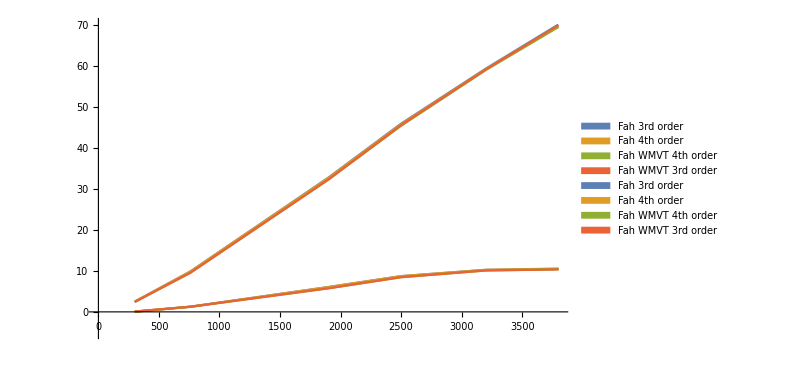

```mathematica
Show[Table[ListLinePlot[{datafahMVT3[[i]],datafahMVT4[[i]],datafahWMVT4[[i]],datafahWMVT3[[i]]},PlotRange->{{0,3800},{-5,70}},PlotLegends->SwatchLegend[{"Fah 3rd order","Fah 4th order","Fah WMVT 4th order","Fah WMVT 3rd order"}]],{i,1,2}],ImageSize->600]
```

```mathematica
Table[Table[mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,2}]//TableForm
Table[Table[mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,2}]//TableForm
```

0.499975 | 0.499627 | 0.481712 | 0.468761 | 0.470297 | 0.458634
0.49951 | 0.489732 | 0.44544 | 0.401394 | 0.405338 | 0.408147

0.499999 | 0.49978 | 0.481384 | 0.470994 | 0.471948 | 0.467047
0.499686 | 0.489571 | 0.425016 | 0.387996 | 0.397327 | 0.388421

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/ZrC_analysis/Data/TI/GibbsBog-nov16_x_free_4_longRun_4.8_4_3_v1v2_noholdcutoffs"];
tiRotFiles={"vol_ZrFitTrue_CFitTrue"};
(*Format:  volume ZrFitted ZrTrue CFitted CTrue
*)
tiRotDataRaw=Table[ReadList[tiRotFiles[[i]],{Number, Number,Number,Number,Number}],{i,1,1}][[1]];
tiRotDataRaw
```

```mathematica
tiRotData=Table[Transpose[{Transpose[tiRotDataRaw][[1]],Transpose[tiRotDataRaw][[1+i]]}],{i,1,4}]
```

{{{4.6583,-0.13083},{4.685,-0.12084},{4.73,-0.10344},{4.759,-0.09285},{4.801,-0.08735},{4.85,-0.08366}},{{4.6583,-0.13278},{4.685,-0.1264},{4.73,-0.1161},{4.759,-0.1098},{4.801,-0.10111},{4.85,-0.09161}},{{4.6583,-0.18384},{4.685,-0.1709},{4.73,-0.14892},{4.759,-0.13462},{4.801,-0.12361},{4.85,-0.11433}},{{4.6583,-0.1848},{4.685,-0.17419},{4.73,-0.15725},{4.759,-0.147},{4.801,-0.133},{4.85,-0.11788}}}

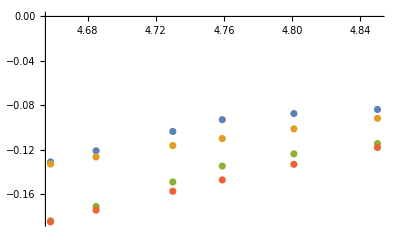

```mathematica
ListPlot@tiRotData[[1;;4]]
```

```mathematica
fits=Table[Fit[tiRotData[[i]],{1,x,x^2,x^3},x],{i,1,4}]
```

{284.571-186.298 x+40.5306 x^2-2.93199 x^3,-6.49901+2.89826 x-0.416483 x^2+0.0188241 x^3,391.854-253.986 x+54.7343 x^2-3.92363 x^3,-19.1849+9.93858 x-1.72754 x^2+0.100811 x^3}

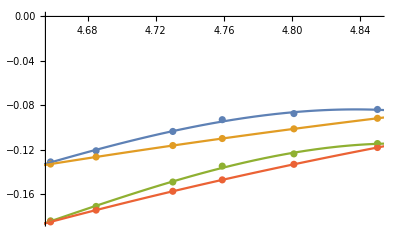

```mathematica
Show[{ListPlot@tiRotData[[1;;4]],Plot[fits,{x,4.6,4.9}]}]
```

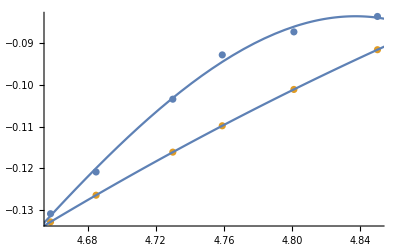

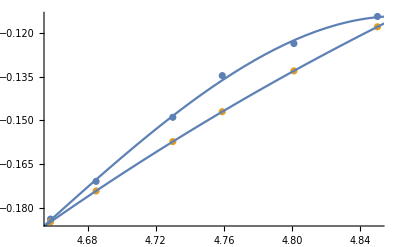

```mathematica
Show[{ListPlot@tiRotData[[1;;2]],Plot[fits[[1;;2]],{x,4.6,4.9}]}]
Show[{ListPlot@tiRotData[[3;;4]],Plot[fits[[3;;4]],{x,4.6,4.9}]}]
```

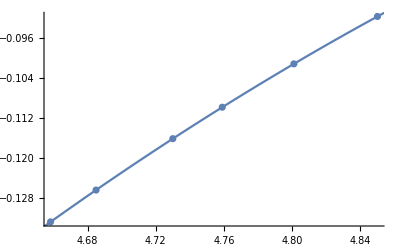

```mathematica
Show[{ListPlot@tiRotData[[2;;2]],Plot[fits[[2;;2]],{x,4.6,4.9}]}]
```

```mathematica
fits[[2]]/.x->4.850//N
```

-0.0916111

```mathematica
vols={4.6583,4.685,4.730,4.759,4.801,4.850}
```

{4.6583,4.685,4.73,4.759,4.801,4.85}

```mathematica
zrMap=Table[Solve[fits[[1]]==Evaluate[fits[[2]]/.x->vols[[i]]//N],x][[2]],{i,1,6}];
cMap=Table[Solve[fits[[3]]==Evaluate[fits[[4]]/.x->vols[[i]]//N],x][[2]],{i,1,6}];
zrMapReverse=Table[Solve[fits[[2]]==Evaluate[fits[[1]]/.x->vols[[i]]//N],x][[1]],{i,1,6}];
cMapReverse=Table[Solve[fits[[4]]==Evaluate[fits[[3]]/.x->vols[[i]]//N],x][[1]],{i,1,6}];


x/.zrMap
x/.cMap
meanMap=0.5Total@{x/.cMap,x/.zrMap}

x/.zrMapReverse
x/.cMapReverse
meanMapReverse=0.5Total@{x/.cMapReverse,x/.zrMapReverse}
```

{4.65498,4.66964,4.69452,4.71099,4.73627,4.77084}

{4.65714,4.67746,4.71111,4.73317,4.76757,4.82214}

{4.65606,4.67355,4.70282,4.72208,4.75192,4.79649}

{4.66435,4.71289,4.79095,4.83463,4.8802,4.89238}

{4.6598,4.69505,4.75489,4.79108,4.83453,4.86129}

{4.66207,4.70397,4.77292,4.81285,4.85736,4.87683}

```mathematica
zrMapReverse=Table[Solve[fits[[2]]==Evaluate[fits[[1]]/.x->vols[[i]]//N],x][[1]],{i,1,6}]
```

{{x→4.66435},{x→4.71289},{x→4.79095},{x→4.83463},{x→4.8802},{x→4.89238}}

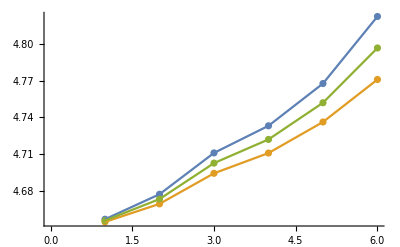

```mathematica
Show[{ListPlot[{x/.cMap,x/.zrMap,meanMap}],ListLinePlot[{x/.cMap,x/.zrMap,meanMap}]}]
```

#### Average the change in FC, to find new volumes

```mathematica
tiRotDataSum=Table[Transpose[{Transpose[tiRotDataRaw][[1]],Transpose[tiRotDataRaw][[1+i]]+Transpose[tiRotDataRaw][[3+i]]}],{i,1,2,1}]
fitsSum=Table[Fit[tiRotDataSum[[i]],{1,x,x^2,x^3},x],{i,1,2}]
```

{{{4.6583,-0.31467},{4.685,-0.29174},{4.73,-0.25236},{4.759,-0.22747},{4.801,-0.21096},{4.85,-0.19799}},{{4.6583,-0.31758},{4.685,-0.30059},{4.73,-0.27335},{4.759,-0.2568},{4.801,-0.23411},{4.85,-0.20949}}}

{676.425-440.284 x+95.265 x^2-6.85562 x^3,-25.6839+12.8368 x-2.14402 x^2+0.119635 x^3}

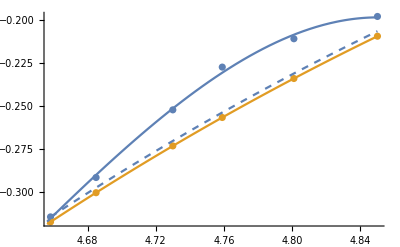

0.00291

```mathematica
Show[{ListPlot@tiRotDataSum,Plot[fitsSum,{x,4.6563,4.850}],Plot[fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]]),{x,4.6583,4.850},PlotStyle->Dashed]}]
```

```mathematica
Table[Solve[fitsSum[[1]]==Evaluate[fitsSum[[2]]/.x->vols[[i]]//N],x][[2]],{i,1,6}]
```

{{x→4.65615},{x→4.67394},{x→4.70375},{x→4.72342},{x→4.7539},{x→4.79881}}

```mathematica
Table[Solve[fitsSum[[2]]==Evaluate[fitsSum[[1]]/.x->vols[[i]]//N],x][[1]],{i,1,6}]
```

{{x→4.6615},{x→4.70173},{x→4.76845},{x→4.80749},{x→4.85182},{x→4.87318}}

#### Linearise the FC vs V dependence

```mathematica
(*y=mx+c
m=deltaFC/deltaV
*)
tiRotDataSum[[1]][[1]][[2]]
tiRotDataSum[[1]][[1]][[1]]
tiRotDataSum[[1]][[-1]][[1]]
tiRotDataSum[[1]][[-1]][[2]]
```

-0.31467

4.6583

4.85

-0.19799

```mathematica
m=(tiRotDataSum[[1]][[-1]][[2]]-tiRotDataSum[[1]][[1]][[2]])/(tiRotDataSum[[1]][[-1]][[1]]-tiRotDataSum[[1]][[1]][[1]])
(*c=y1-mx1*)
c=tiRotDataSum[[1]][[1]][[2]]-m*tiRotDataSum[[1]][[1]][[1]]
```

0.608659

-3.14999

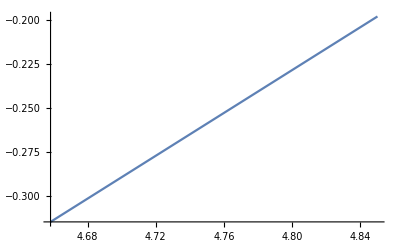

```mathematica
FC[V_]:=m*V+c
Plot[Evaluate@FC[x],{x,4.6583,4.850}]
```

```mathematica
sumFCs=Transpose[tiRotDataSum[[1]]][[2]]
(*Mapping the FCs to the linearised FC(V) function provides these new volumes:*)
linVols=Table[Solve[FC[x]==sumFCs[[i]],{x}][[1]],{i,1,6}]
Table[linVols[[i]][[1]][[2]],{i,1,6}]
```

{-0.31467,-0.29174,-0.25236,-0.22747,-0.21096,-0.19799}

{{x→4.6583},{x→4.69597},{x→4.76067},{x→4.80157},{x→4.82869},{x→4.85}}

{4.6583,4.69597,4.76067,4.80157,4.82869,4.85}

#### Linearise using the DFT gradient, but potential starting point

```mathematica
(*y=mx+c
m=deltaFC/deltaV
*)
tiRotDataSum[[2]][[1]][[2]]
tiRotDataSum[[2]][[1]][[1]]
tiRotDataSum[[2]][[-1]][[1]]
tiRotDataSum[[2]][[-1]][[2]]
```

-0.31758

4.6583

4.85

-0.20949

```mathematica
mDFT=(tiRotDataSum[[2]][[-1]][[2]]-tiRotDataSum[[2]][[1]][[2]])/(tiRotDataSum[[2]][[-1]][[1]]-tiRotDataSum[[2]][[1]][[1]])
```

0.56385

-2.94125

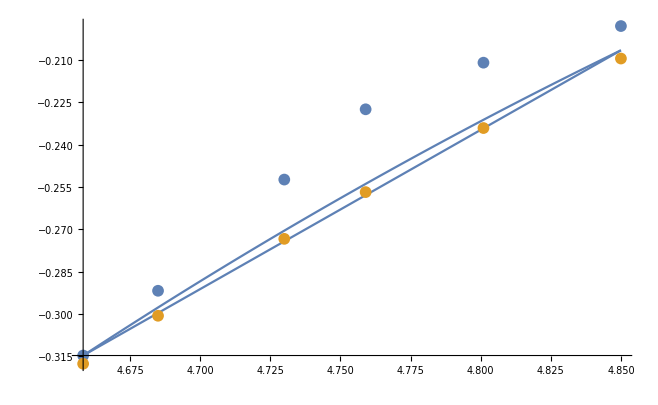

```mathematica
(*c=y1-mx1*)
cDFT=tiRotDataSum[[1]][[1]][[2]]-mDFT*tiRotDataSum[[1]][[1]][[1]]
FCdft[V_]:=mDFT*V+cDFT
Show[{Plot[Evaluate@FCdft[x],{x,4.6583,4.850},PlotRange->All],ListPlot@tiRotDataSum,Plot[fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]]),{x,4.6583,4.850},PlotRange->All]}]
```

```mathematica
FCdft[x]
fcDFTnonlinear=fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]])
```

-2.94125+0.56385 x

-25.681+12.8368 x-2.14402 x^2+0.119635 x^3

### Linear solutions with DFT gradient

```mathematica
linDFTVols=Table[Solve[FCdft[x]==sumFCs[[i]],{x}][[1]],{i,1,6}]
Table[linDFTVols[[i]][[1]][[2]],{i,1,6}]
```

{{x→4.6583},{x→4.69897},{x→4.76881},{x→4.81295},{x→4.84223},{x→4.86523}}

{4.6583,4.69897,4.76881,4.81295,4.84223,4.86523}

### Non-linear solutions with DFT gradients

```mathematica
nonlinDFTVols=Table[Solve[fcDFTnonlinear==sumFCs[[i]],{x}][[1]],{i,1,6}]
Table[nonlinDFTVols[[i]][[1]][[2]],{i,1,6}]
```

{{x→4.65831},{x→4.69454},{x→4.76175},{x→4.80816},{x→4.84099},{x→4.86809}}

{4.65831,4.69454,4.76175,4.80816,4.84099,4.86809}

#### Linear shift up, not sideways:

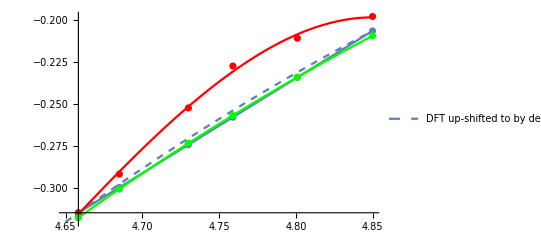

```mathematica
Show[{Plot[FCdft[x],{x,4.6583,4.850},PlotRange->All,PlotLegends->"DFT"],ListPlot[Transpose@{vols,FCdft[vols]}],Plot[fcDFTnonlinear,{x,4.65,4.85},PlotStyle->Dashed,PlotLegends->{"DFT up-shifted to by deltaFC at V0"}],Plot[fitsSum,{x,4.6563,4.850},PlotStyle->{Red,Green}],ListPlot[tiRotDataSum,PlotStyle->{Red,Green}]}]
```

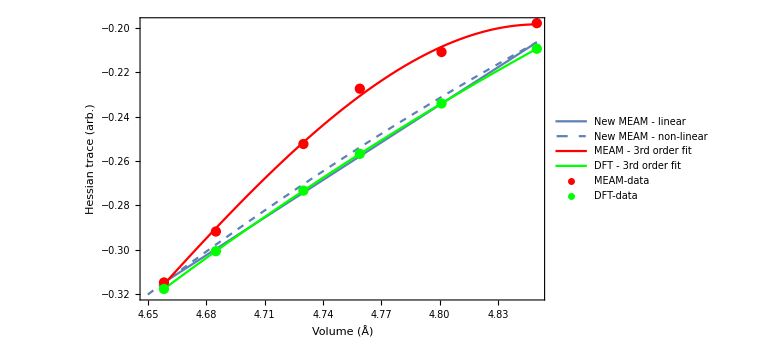

```mathematica
Show[{Plot[FCdft[x],{x,4.6583,4.850},PlotRange->All,PlotLegends->{"New MEAM - linear"},Frame->True,FrameLabel->{"Volume (Å)","Hessian trace (arb.)"},ImageSize->Large],Plot[fcDFTnonlinear,{x,4.65,4.85},PlotStyle->Dashed,PlotLegends->{"New MEAM - non-linear"}],Plot[Evaluate@fitsSum,{x,4.6563,4.850},PlotStyle->{Red,Green},PlotLegends->{"MEAM - 3rd order fit","DFT - 3rd order fit"}],ListPlot[tiRotDataSum,PlotStyle->{Red,Green},PlotLegends->{"MEAM-data","DFT-data"}]}]
```

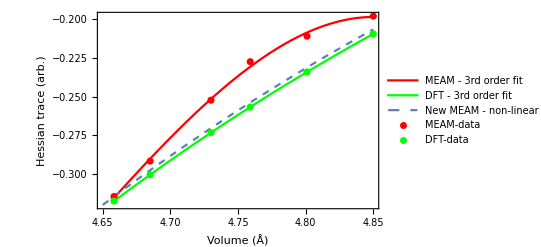

```mathematica
Show[{Plot[Evaluate@fitsSum,{x,4.6563,4.850},PlotStyle->{Red,Green},PlotRange->All,PlotLegends->{"MEAM - 3rd order fit","DFT - 3rd order fit"},Frame->True,FrameLabel->{"Volume (Å)","Hessian trace (arb.)"}],Plot[fcDFTnonlinear,{x,4.65,4.85},PlotStyle->Dashed,PlotLegends->{"New MEAM - non-linear"},ImageSize->Large],ListPlot[tiRotDataSum,PlotStyle->{Red,Green},PlotLegends->{"MEAM-data","DFT-data"}]}]
```

```mathematica
Table[FCdft[vols][[i]]/Transpose[tiRotDataSum[[1]]][[2]][[i]],{i,1,6}]
```

{1.,1.02699,1.08671,1.13373,1.1102,1.04339}

```mathematica
(fcDFTnonlinear/.x->vols)/Transpose[tiRotDataSum[[1]]][[2]]
```

{1.00003,1.02029,1.07171,1.11615,1.0959,1.0434}

```mathematica
ListPlot[Transpose@{vols,FCdft[vols]}]
```